# The Problem of Distributed Consensus

In preparation for a conference entitled “Distributed Consensus with Cellular Automata and Related Systems” that we’re organizing with NKN (= “New Kind of Network”) I decided to explore the problem of distributed consensus using methods from A New Kind of Science (yes, NKN “rhymes” with NKS) as well as from the Wolfram Physics Project.

## A Simple Example

```mathematica
BlockRandom[SeedRandom[77];Module[{pts = RandomPointConfiguration[HardcorePointProcess[0.09, 2, 2], Rectangle[{0, 0}, {40, 40}]]["Points"],clrs}, 
clrs = Table[RandomChoice[{.65,.35}->{Hue[0.15, 0.72, 1],Hue[0.98, 1, 0.8200000000000001]}], Length[pts]];Graphics[{EdgeForm[Gray],Table[Style[Disk[pts[[n]]],clrs[[n]]], {n, Range[Length[pts]]}]}]]]
```

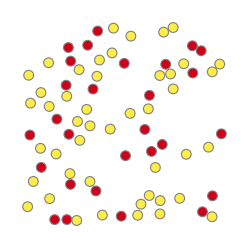

Consider a collection of “nodes”, each one of two possible colors. We want to determine the majority or “consensus” color of the nodes, i.e. which color is the more common among the nodes.

One obvious method to find this “majority” color is just sequentially to visit each node, and tally up all the colors. But it’s potentially much more efficient if we can use a distributed algorithm, where we’re running computations in parallel across the various nodes.

One possible algorithm works as follows. First connect each node to some number of neighbors. For now, we’ll just pick the neighbors according to the spatial layout of the nodes:

```mathematica
ConsensusState[points_, colors_, nn_:5] := NearestNeighborGraph[points,nn,DirectedEdges->True, DistanceFunction->EuclideanDistance,VertexStyle -> MapThread[Rule, {points, colors}], VertexSize -> 0.75, EdgeStyle -> Gray]
```

```mathematica
BlockRandom[SeedRandom[77];Module[{pts = RandomPointConfiguration[HardcorePointProcess[0.09, 2, 2], Rectangle[{0, 0}, {40, 40}]]["Points"],clrs},
clrs = Table[RandomChoice[{.65,.35}->{Hue[0.15, 0.72, 1],Hue[0.98, 1, 0.8200000000000001]}], Length[pts]]; 
ConsensusState[pts, clrs]]]
```

-Graphics-

The algorithm works in a sequence of steps, at each step updating the color of each node to be whatever the “majority color” of its neighbors is. In the case shown, this procedure converges after a few steps to make all nodes have the “majority color” (which here is yellow)—or in effect “agree” on what the majority color is:

```mathematica
ConsensusState[points_, colors_, nn_:5] := NearestNeighborGraph[points,nn,DirectedEdges->True, DistanceFunction->EuclideanDistance,VertexStyle -> MapThread[Rule, {points, colors}], VertexSize -> 0.75, EdgeStyle -> Gray]
```

```mathematica
NodeDependencies[points_, nn_:5]:= Table[n-> Flatten[Map[Position[points, #]&,VertexOutComponent[NearestNeighborGraph[points,nn, DirectedEdges -> True, DistanceFunction->EuclideanDistance], points[[n]], {1}]]], {n, Range[Length[points]]}]
```

```mathematica
SynchronousStepNewColors[dependencies_, colors_]:= 
Flatten[Map[With[{neighbors = Sort[Counts[Part[colors, Last[#]]], Greater]},
If[DuplicateFreeQ[Values[neighbors]],
First[Keys[neighbors]], 
colors[[First[#]]]]]&, dependencies]]
```

```mathematica
GraphicsGrid[Partition[BlockRandom[SeedRandom[77];Module[{pts = RandomPointConfiguration[HardcorePointProcess[0.09, 2, 2], Rectangle[{0, 0}, {40, 40}]]["Points"],clrslist, highlights},
clrslist=NestList[SynchronousStepNewColors[NodeDependencies[pts], #]&, Table[RandomChoice[{.65,.35}->{Yellow,Red}], Length[pts]], 7];
MapIndexed[With[{colors = #}, Graph[ConsensusState[pts, colors],ImageSize->150]] &,clrslist]
]],4],ImageSize-> 600]
```

-Graphics-

This is a simple example of a distributed consensus algorithm in action. The challenge we’ll discuss here is to find the most efficient and robust such algorithms.

## The Background

In any decentralized system with computers, people, databases, measuring devices or anything else one can end up with different values or results at different “nodes”. But for all sorts of reasons one often wants to agree on a single “consensus” value, that one can for example use to “make a decision and go on to the next step”.

Blockchains are one example of systems that need this kind of consensus to “finish each block”. Traditional blockchains achieve consensus through what amounts to a centralized mechanism (even though there are multiple “decentralized” copies of the blockchain that is produced).

But there are now starting to be distributed analogs of blockchains that need distributed consensus algorithms. And the main inspiration for the algorithms being developed are cellular automata (and to a lesser extent spin systems in statistical mechanics).

One issue is to make the algorithm as efficient as possible. Another is to make it as robust as possible, for example with respect to random noise—or malicious errors—introduced at or between nodes.

The amount of random noise can be thought of as something like a temperature. And at least in certain cases there can be a “phase transition” so that below a certain “temperature” there can be zero effect on the consensus output—implying robustness to a certain level of noise.

Some of what happens can be studied using methods from standard equilibrium statistical physics. But in most cases one has to take account of the time dependence or evolution of the system, leading to something like a probabilistic cellular automaton (closely related to directed percolation, dynamic spin systems, etc.).

As I’ll discuss below, in the early days of computing, there was great interest in synthesizing reliable systems out of unreliable components. And by the 1960s there was study first of neural nets and then of cellular automata with probabilistic elements. And some surprising results were obtained that showed that cellular automata could be set up that would be robust with respect to a certain nonzero level of noise.

One feature of cellular automata is that their elements are all assumed to be arranged in a definite array, and to be updated in parallel "at the same time" in a sequence of steps. For many practical applications, however, one instead wants elements that are connected in some kind of graph (that may even be dynamic), and that are in general updated asynchronously, in no particular order.

The simple example we gave above is a graph cellular automaton: the connections between elements are defined by a graph, but the updates are all done synchronously at each step. In the past, it's been difficult to analyze the more general setup where there is no rigid notion of either space or time. But this is exactly the setup in our new Physics Project, and so there's now the potential to use its formalism and results (as well as intuition imported from physics) to make further progress.

## Deterministic Cellular Automata

To start getting some intuition for the problem of distributed consensus, let’s consider the following very simple setup. We have a line of cells, each with one of two possible colors. Then we update the colors of these cells in a sequence of steps, based on a local rule which depends on neighboring cells. This system is a one-dimensional cellular automaton—of the kind that I started studying more than 40 years ago.

We imagine that the initial condition involves a fraction p of red cells. We want all the cells to turn red if p > 1/2, and all of them to turn yellow if p < 1/2. The most obvious rule that might achieve this would just replace each cell by the majority color in its neighborhood (rule 232 in my numbering scheme):

```mathematica
RulePlot[CellularAutomaton[232],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange]
```

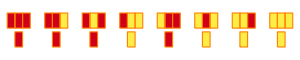

Here’s what rule 232 does starting with 70% red cells in a “random configuration”:

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[CellularAutomaton[232,RandomChoice[{.7,.3}->{1,0},120],20],Mesh->True,ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange]]
```

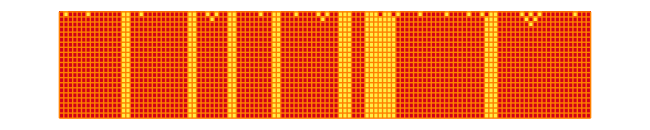

As we can see, it manages to achieve a little “local consensus”, but ultimately it’s not successful at reaching a “global consensus” in which all cells are the same color.

And we might imagine that there’d be no rule for a 1D deterministic cellular automaton that would lead to global consensus (or be able to solve the “density classification problem” of deciding whether the density of initial red cells is above or below 50%). But it turns out that this isn't true. And for example in 1978 the following “radius 3” rule (operating on size-7 neighborhoods) was constructed (the “GKL rule”):

```mathematica
{l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c≥2,1,0]
```

{l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c≥2,1,0]

Here’s what this rule does with 60% red cells:

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/.{l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c≥2,1,0],2],2,3},RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False]]
```

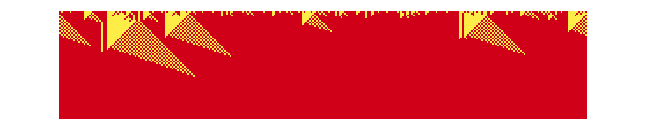

And here’s what it does with 40% red cells:

```mathematica
BlockRandom[SeedRandom[569];ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/.{l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c≥2,1,0],2],2,3},RandomChoice[{.4,.6}->{1,0},300],60],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False]]
```

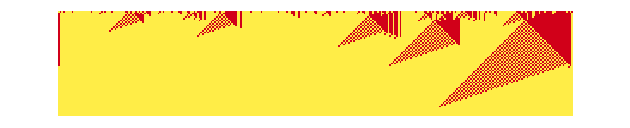

In both these cases, the rule successfully achieves “global consensus”. And in fact one can prove that this rule will always do this, at least after sufficiently many steps. Here’s a plot of how the density evolves as a function of time for different initial densities:

```mathematica
data = ParallelTable[If[p==.5,Nothing,MeanAround/@Transpose[Table[Mean/@CellularAutomaton[{FromDigits[Tuples[{1,0},7]/.{l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c≥2,1,0],2],2,3},RandomChoice[{p,1-p}->{1,0},5000],200],200]]],{p,.3,.7,.05}];
```

```mathematica
ListLinePlot[MapThread[Callout[#1, Row[{Style["p",Italic],"=",#2}]]&,{data, Cases[Range[.3, .7, .05], Except[0.5]]}]]
```

-Graphics-

And what we see is that there’s what looks like a phase transition: for initial density p < 0.5, the final density is exactly 0, while for initial density p > 0.5, it’s instead exactly 1.

What happens precisely at p = 0.5? In a sense the cellular automaton “can’t make up its mind” and on an infinite line it generates an infinite nested sequence of domains that alternate between 0 and 1:

```mathematica
BlockRandom[SeedRandom[24425];ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/.{l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c≥2,1,0],2],2,3},RandomChoice[{.5,.5}->{1,0},1000],500],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False]]
```

-Graphics-

This nested structure is typical of what’s seen in critical phenomena in statistical physics, and in fact cellular automata like this are the very simplest examples of “true” phase transitions that I know. (Like other phase transitions, these don’t become “sharp” except in infinite systems. In typical statistical mechanics one doesn’t get phase transitions in 1D, but that’s a consequence of the assumption of microscopic reversibility, which doesn’t apply to cellular automata like this.)

So what other cellular automaton rules achieve consensus like this? There are no radius-1 rules that work. And if one searches all 2^32 radius-2 rules (as I did for A New Kind of Science), the best one finds are a handful of examples that achieve “approximate consensus” in the sense that most, though not all, of the cells go to the “majority value” (this is the r = 2 rule 4196304428, for p = 0.6):

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[CellularAutomaton[{4196304428,2,2},RandomChoice[{.6,.4}->{1,0},500],200],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False]]
```

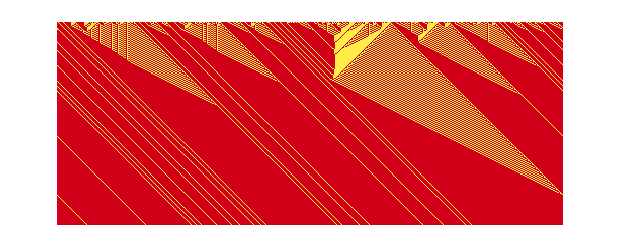

By the way, among radius-1 rules, there is rule 184 (often used as a basic model of road traffic flow), which doesn’t achieve consensus on “overall density”, but does do so with respect to left- and right-moving stripes, here with the nested pattern generated when p = 0.5:

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[CellularAutomaton[184,RandomChoice[{1,0},400],180],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False]]
```

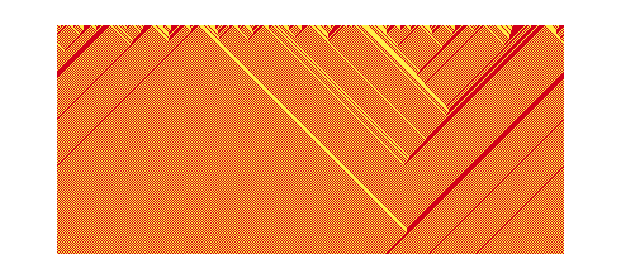

What about “achieving consensus faster”? Here’s a comparison of our original GKL rule with another radius-3 rule (discovered by genetic programming methods) whose average consensus time is shorter:

```mathematica
Column[BlockRandom[SeedRandom[24125];ArrayPlot[CellularAutomaton[#,RandomChoice[{.48,.52}->{1,0},800],180],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False,ImageSize->{650,Automatic}]]&/@{{339789091192587366278221041213531750560,2,3},{339841014953466429132970652455676805280,2,3}}]
```

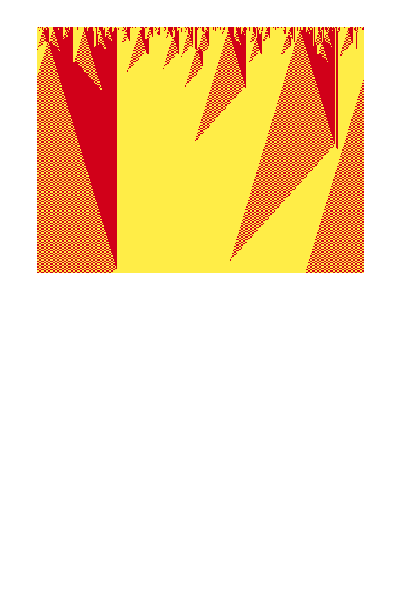

It’s not known in general what the “fastest” radius-3 rule is. The two rules above have the feature that they “do their job” in a fairly “simple-looking” way. But there are also rules like the following that do their job in a “more ornate” way:

```mathematica
Column[BlockRandom[SeedRandom[24125];ArrayPlot[CellularAutomaton[#,RandomChoice[{.48,.52}->{1,0},800],240],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False,ImageSize->{650,Automatic}]]&/@{{337607298446901146542393000444934784552,2,3},{338557163619953682141694933300561896488,2,3},{313421633154342960352882914658469183496,2,3}}]
```

-Graphics-

Human-engineered rules (like the first one above) almost inevitably work in simpler and more “understandable” ways. But experience elsewhere (such as with optimal sorting networks) suggests that optimal rules will often be ones that don’t look simple in their behavior, and that can’t realistically be constructed by standard engineering methods, and essentially just have to be found “experimentally” by searching the computational universe of possible rules.

A notable feature of particularly the earlier rules we looked at is that they show a small number of types of very distinct “domains” with definite walls or boundaries between them.  And in many ways such walls can be thought of as being like localized structures, “defects” or “particles”.  But for our purposes here what tends to be important is whether these particles move around, and whether they annihilate each other to leave a uniform “consensus” final state.
In the simple majority rule it’s inevitable that there are static domain walls:

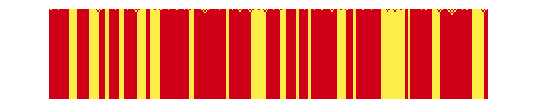

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[CellularAutomaton[232,RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange,Frame->None]]
```

The reason is that as soon as a domain is larger than the cellular automaton neighborhood, a cell at the boundary of the domain will inevitably see a balanced number of cells of each color on the two sides of the boundary.  So the cell itself will act as a “tie breaker”, and will always decide to stay its own color---thereby making the domain boundary stay as it is.

So what if we have a longer-range rule, that samples more distant cells?  With range-2 (i.e. a 5-cell neighborhood) “wrong domains” with widths below 4 disappear:

```mathematica
majrn[n_]:=FromDigits[If[Total[#]>n/2,1,0]&/@Tuples[{1,0},n],2]
```

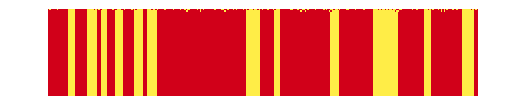

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[CellularAutomaton[{majrn[5],2,{{-2},{-1},{0},{1},{2}}},RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange]]
```

Things work a bit better if the cells being sampled aren’t adjacent, but are for example in the pattern □-□□-□-□:

```mathematica
majrn[n_]:=FromDigits[If[Total[#]>n/2,1,0]&/@Tuples[{1,0},n],2]
```

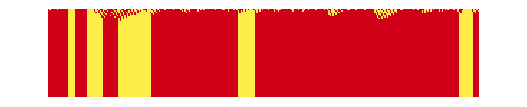

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[CellularAutomaton[{majrn[5],2,{{-3},{-1},{0},{2},{4}}},RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange]]
```

But no finite-size sampling with the pure majority rule will remove all domains.  What about the GKL rule?  This rule actually only samples 5 cells, but its “extremities” are at distance 3.  So can we “improve” it by having it sample more distant cells?

Here’s a comparison of a few cases (the first one is the original):

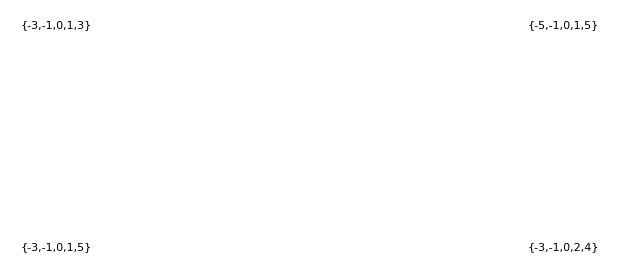

```mathematica
GraphicsGrid[Partition[Labeled[BlockRandom[SeedRandom[567];ArrayPlot[CellularAutomaton[{4177065992,2,List/@#},RandomChoice[{.6,.4}->{1,0},300],100],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange,ImageSize->300]],Style[#,11]]&/@{{-3,-1,0,1,3},{-5,-1,0,1,5},{-3,-1,0,1,5},{-3,-1,0,2,4}},2]]
```

Here we’ve only discussed cellular automata with two possible colors for each cell.  We could also consider rules that involve other “helper” colors that either disappear before the final state is reached, or define additional consensus states.

## But Does It Always Work?

We’ve seen that there are 1D cellular automata that—at least in the examples we’ve looked at—achieve “majority consensus”. But given a particular rule, will it always reach consensus, or are there exceptions?

As a first way to get a well-defined version of that question, we can consider finite cellular automata, say with a total of n cells, and cyclic boundary conditions. There are a total of 2^n possible configurations in this case, and we can represent all possible paths of evolution of the cellular automaton using a state transition graph.

Here's the graph for the GKL rule we discussed above, for the case n = 5. Each node in the graph is colored according to whether its "red-cell fraction" is above or below 1/2. And what we see in this case is "perfect density classification" or "perfect consensus", with all states correctly leading to all-red or all-yellow states:

```mathematica
With[{n=5},Graph[#->CellularAutomaton[{339789091192587366278221041213531750560,2,3}][#]&/@Tuples[{1,0},n],VertexStyle->(#->If[Mean[#]>1/2,Hue[0.98, 1, 0.8200000000000001], Hue[0.15, 0.72, 1]]&/@Tuples[{1,0},n]),GraphLayout->{"VertexLayout"->"LayeredDigraphEmbedding","PackingLayout"->"LayeredLeft"}, EdgeStyle -> Hue[0.75, 0, 0.35]]]
```

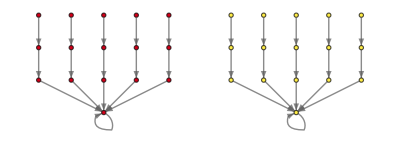

But as soon as we look, for example, at n = 7, we immediately see a problem:

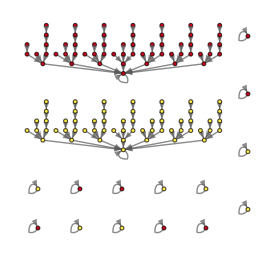

```mathematica
With[{n=7},Graph[#->CellularAutomaton[{339789091192587366278221041213531750560,2,3}][#]&/@Tuples[{1,0},n],VertexStyle->(#->If[Mean[#]>1/2,Hue[0.98, 1, 0.8200000000000001], Hue[0.15, 0.72, 1]]&/@Tuples[{1,0},n]),VertexSize->.4,GraphLayout->{"VertexLayout"->"LayeredDigraphEmbedding","PackingLayout"->"Layered"}, EdgeStyle -> Hue[0.75, 0, 0.35]]]
```

The states

```mathematica
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/.{l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c≥2,1,0],2],2,3},#,4],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False,Mesh->True,MeshStyle->Orange,ImageSize->Tiny]&/@{{0,0,1,0,0,1,1},{0,0,1,1,0,1,1}}
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

and their cyclic variations “get stuck” and do not achieve consensus. At size 11 there’s another issue: now a few states that should have achieved “consensus 1” actually go to “consensus 0”:

```mathematica
With[{size11=Graph[#->CellularAutomaton[{339789091192587366278221041213531750560,2,3}][#]&/@Tuples[{1,0},11],VertexStyle->(#->If[Mean[#]>1/2,Hue[0.98, 1, 0.8200000000000001], Hue[0.15, 0.72, 1]]&/@Tuples[{1,0},11]),VertexSize->.4, EdgeStyle -> Hue[0.75, 0, 0.35]]},Grid[{{Show[Graph[# , AspectRatio-> 1/3], ImageSize-> {300, Automatic}]&[WeaklyConnectedGraphComponents[size11][[1]]], With[{stuck=Catenate[EdgeList/@Drop[WeaklyConnectedGraphComponents[size11], 2]]},Show[Graph[stuck,VertexStyle->(#->If[Mean[#]>1/2,Hue[0.98, 1, 0.8200000000000001], Hue[0.15, 0.72, 1]]&/@(First/@stuck)),EdgeStyle ->Hue[0.75, 0, 0.35], GraphLayout->{"VertexLayout"->"LayeredDigraphEmbedding","PackingLayout"->"NestedGrid"}], ImageSize -> {Automatic, 200}]]}, {Show[Graph[# , AspectRatio-> 1/3], ImageSize-> {300, Automatic}]&[WeaklyConnectedGraphComponents[size11][[2]]], SpanFromAbove}}, Alignment -> {Center, Center}]]
```

-Graphics-

The states that “get to the wrong consensus” here all turn out to be cyclic variations of the following

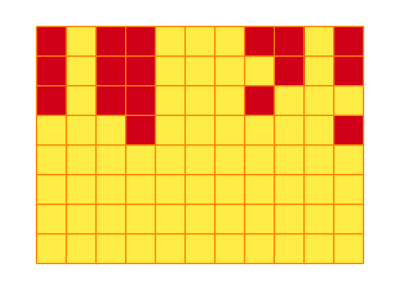
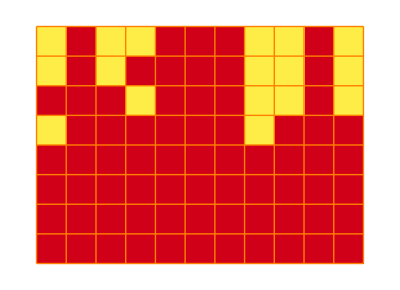

{-Graphics-,-Graphics-}

```mathematica
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/.{l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c≥2,1,0],2],2,3},#,7],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False,Mesh->True,MeshStyle->Orange,ImageSize->Tiny]&/@{{1,0,1,1,0,0,0,1,1,0,1}, {0,1,0,0,1,1,1,0,0,1,0}}
```

where in the first case there are 6 Hue[0.98, 1, 0.8200000000000001] cells and 5 Hue[0.15, 0.72, 1], yet the final state is all Hue[0.15, 0.72, 1], and in the second case it’s the other way around.

And it turns out that there’s actually a general problem: one can prove that there’s no rule that can perfectly achieve “majority consensus” on a finite array with cyclic boundary conditions.

What about on an infinite array? Here it’s possible to achieve “perfect majority consensus” for all but a set of “special initial conditions” with measure 0. An example of such a “special initial condition” is an infinite repetition of either of the two blocks shown above. These initial conditions—instead of going to consensus—will just remain fixed with time.

If initial conditions are generated “at random”, with the value of each cell being chosen according to certain fixed probabilities, then there’s effectively zero probability of getting one of the “exception” initial conditions. And even though the “tapers” might be arbitrarily long, there’s no chance of not eventually reaching a consensus state.

But this conclusion depends on the idea that initial conditions are really generated “at random”. If, for example, they were generated by a definite program, then though the initial conditions might seem “statistically random” with respect to certain tests, it doesn’t mean that they won’t give special weight to the “exceptional” initial conditions.

## Beyond One Dimension

In one dimension one can explain the fact that certain configurations “get stuck” and don’t achieve consensus by saying that in 1D effects can’t “get around each other”. But in 2D there is no such constraint.

So then what about the "pure 2D majority rule" (totalistic code 56):

```mathematica
RulePlot[CellularAutomaton[<|"Dimension"->2,"Neighborhood"->5,"TotalisticCode"->56|>],ColorFunction->(Blend[{RGBColor@Hue[0.15, 0.72, 1],RGBColor@Hue[0.98, 1, 0.8200000000000001]},#]&),MeshStyle->Orange]
```

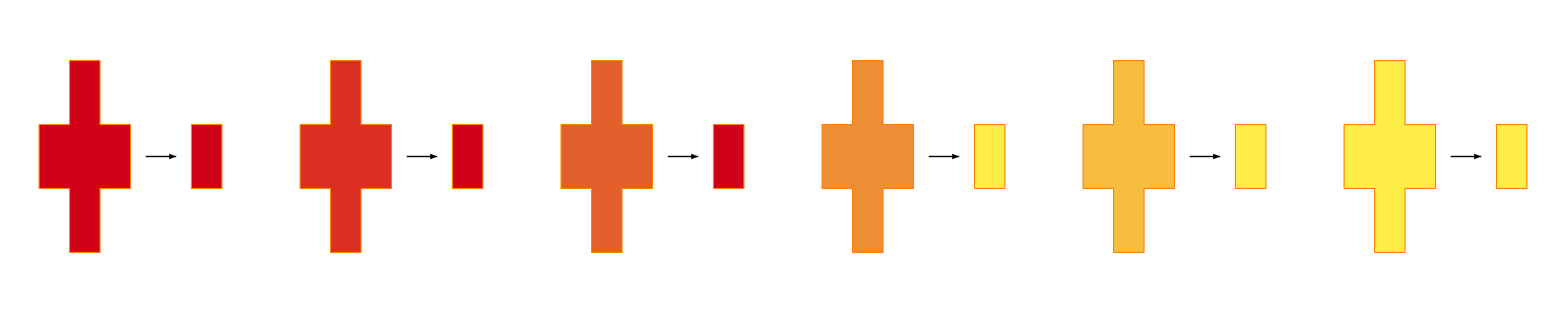

Starting say from 30% 1s we again see that things get stuck:

```mathematica
GraphicsRow[BlockRandom[SeedRandom[23424];ArrayPlot[#,ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},ImageSize->120,Frame->False,Mesh->True,MeshStyle->Orange]&/@CellularAutomaton[<|"Dimension"->2,"Neighborhood"->5,"TotalisticCode"->56|>,RandomChoice[{.3,.7}->{1,0},{30,30}],{{0,4},All}]]]
```

-Graphics-

Here is the corresponding evolution shown in 3D, with time going down:

```mathematica
BlockRandom[SeedRandom[23424];ArrayPlot3D[#,ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange]&@CellularAutomaton[<|"Dimension"->2,"Neighborhood"->5,"TotalisticCode"->56|>,RandomChoice[{.3,.7}->{1,0},{30,30}],{{0,10},All}]]
```

-Graphics3D-

But here is another rule (9-neighbor totalistic code 976):

```mathematica
GraphicsGrid[Partition[BlockRandom[SeedRandom[23424];ArrayPlot[#,ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},ImageSize->80,Frame->False]&/@(CellularAutomaton[<|"Dimension"->2,"Neighborhood"->9,"TotalisticCode"->976|>,RandomChoice[{.45,.55}->{1,0},{30,30}],{{0,17},All}])],7]]
```

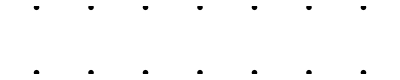

And now what we see is that in this case blob-like domains of the “minority color” get left over, but gradually get smaller. We can see the phenomenon in 3D:

```mathematica
BlockRandom[SeedRandom[23424];ArrayPlot3D[#,ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]}]&@(CellularAutomaton[<|"Dimension"->2,"Neighborhood"->9,"TotalisticCode"->976|>,RandomChoice[{.45,.55}->{1,0},{50,50}],{{0,40},All}])]
```

-Graphics3D-

Looking at a spacetime slice in the center, and letting more distant cells “recede into the fog”, we see what looks like “diffusive” behavior, with domain walls in effect executing random walks that eventually annihilate:

```mathematica
BlockRandom[SeedRandom[23424];ArrayPlot[Mean/@Transpose[MapIndexed[#1*(1.6^-Last[#2])&,CellularAutomaton[<|"Dimension"->2,"TotalisticCode"->976,"Neighborhood"->9|>,RandomChoice[{.45,.55}->{1,0},{220,40}],80],{-1}],2<->3],ColorFunction->(Blend[{RGBColor@Hue[0.15, 0.72, 1],RGBColor@Hue[0.98, 1, 0.8200000000000001]},#]&),Frame->False]]
```

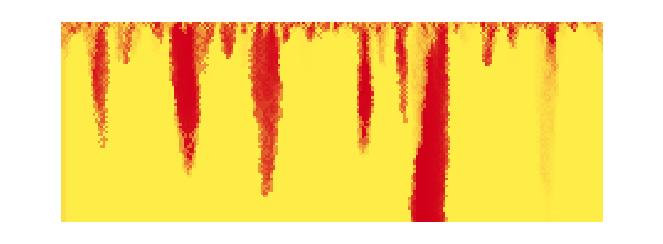

The rule we just saw is close to the majority rule on a 9-cell 3×3 region, except for totals 4 and 5, which are taken to give 1 and 0 rather than 0 and 1.  If we use the pure majority rule on the 3×3 region it gets stuck:

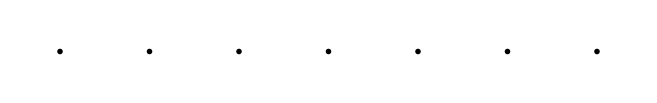

```mathematica
GraphicsGrid[Partition[BlockRandom[SeedRandom[23424];ArrayPlot[#,ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},ImageSize->80,Frame->False]&/@(CellularAutomaton[<|"Dimension"->2,"Neighborhood"->9,"TotalisticCode"->992|>,RandomChoice[{.45,.55}->{1,0},{30,30}],{{0,8},All}])],7]]
```

But it turns out to be straightforward to find 2D majority rules that do not get stuck.  In fact, basically any majority rule that samples cells in an asymmetric way will work.

As an example, consider a rule that samples the following cells in each 3×3 neighborhood:

```mathematica
majplot[offsets_]:=ArrayPlot[Reverse[Transpose[SparseArray[(2+offsets)->1,{3,3}]]],Mesh->True,ImageSize->40]
```

```mathematica
majplot[{{0, 1}, {1, 0}, {0, 0}}]
```

-Graphics-

Here is the 3D evolution of this rule starting from 45% 1s:

```mathematica
BlockRandom[SeedRandom[23424];ArrayPlot3D[#,ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]}]&@(CellularAutomaton[{{{_,a_,_},{_,b_,c_},{_,_,_}}:>If[a+b+c≥2,1,0]},RandomChoice[{.45,.55}->{1,0},{50,50}],{{0,80},All}])]
```

-Graphics3D-

And here is what a spacetime slice looks like:

```mathematica
BlockRandom[SeedRandom[23424];ArrayPlot[Mean/@Transpose[MapIndexed[#1*(1.6^-Last[#2])&,CellularAutomaton[{{{_,a_,_},{_,b_,c_},{_,_,_}}:>If[a+b+c≥2,1,0]},RandomChoice[{.45,.55}->{1,0},{220,40}],60],{-1}],2<->3],ColorFunction->(Blend[{RGBColor@Hue[0.15, 0.72, 1],RGBColor@Hue[0.98, 1, 0.8200000000000001]},#]&),Frame->False]]
```

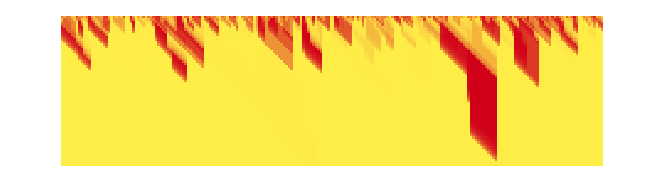

The behavior as a function of the initial density shows a clear transition at 50%:

```mathematica
Row[ParallelTable[BlockRandom[SeedRandom[23424];Labeled[ArrayPlot[Mean/@Transpose[MapIndexed[#1*(1.6^-Last[#2])&,CellularAutomaton[{{{_,a_,_},{_,b_,c_},{_,_,_}}:>If[a+b+c≥2,1,0]},RandomChoice[{p,1-p}->{1,0},{60,40}],60],{-1}],2<->3],ImageSize->72,ColorFunction->(Blend[{RGBColor@Hue[0.15, 0.72, 1],RGBColor@Hue[0.98, 1, 0.8200000000000001]},#]&),Frame->False],Style[PercentForm[p],11]]],{p,.3,.7,.05}]]
```

-Graphics-

Here are results for different samplings of cells in the 3×3 neighborhood; all successfully achieve consensus:

```mathematica
MajorityRule[offsets_]:=With[{n=Length[offsets]},{FromDigits[If[#>n/2,1,0]&/@Reverse[Range[0,n]],2],{2,1},offsets}]
```

```mathematica
majrow[oo_]:=Row[BlockRandom[SeedRandom[23424];{majplot[oo],ArrayPlot3D[#,ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},ImageSize->220]&@(CellularAutomaton[MajorityRule[oo],RandomChoice[{.45,.55}->{1,0},{50,50}],{{0,60},All}]),ArrayPlot[Mean/@Transpose[MapIndexed[#1*(1.6^-Last[#2])&,CellularAutomaton[MajorityRule[oo],RandomChoice[{.45,.55}->{1,0},{100,60}],60],{-1}],2<->3],ColorFunction->(Blend[{RGBColor@Hue[0.15, 0.72, 1],RGBColor@Hue[0.98, 1, 0.8200000000000001]},#]&),Frame->False,ImageSize->300]}],Spacer[25]]
```

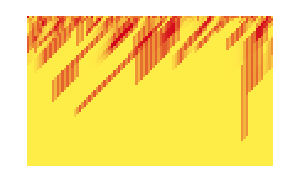
-Graphics--Graphics3D--Graphics-

```mathematica
majrow[{{1,-1},{1,1},{0,0}}]
```

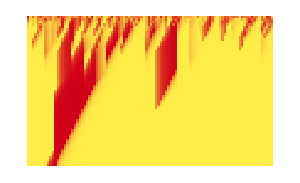
-Graphics--Graphics3D--Graphics-

```mathematica
majrow[{{0,-1},{1,1},{0,0}}]
```

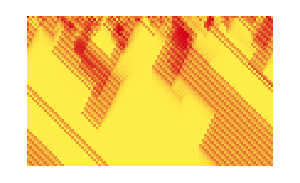
-Graphics--Graphics3D--Graphics-

```mathematica
majrow[{{0,-1},{1,1},{-1,0}}]
```

```mathematica
majrow[{{0,1},{-1,0},{1,1},{1,0},{0,-1}}]
```

-Graphics--Graphics3D--Graphics-

```mathematica
majplot[{{-1,0},{0,0},{1,0},{0,1},{0,-1}}]
```

-Graphics-

With our original 5-cell “symmetrical” neighborhood   we can get very similar behavior by setting things up like the 1D GKL rule:

```mathematica
{{{_,a_,_},{b_,c_,d_}, { _, e_, _}}:>If[If[c==0,a+b, d+e]+c≥2,1,0]}
```

```mathematica
{BlockRandom[SeedRandom[23424];ArrayPlot3D[#,ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]}]&@(CellularAutomaton[{{{_,a_,_},{b_,c_,d_}, { _, e_, _}}:>If[If[c==0,a+b, d+e]+c≥2,1,0]},RandomChoice[{.45,.55}->{1,0},{50,50}],{{0,80},All}])],BlockRandom[SeedRandom[23424];ArrayPlot[Mean/@Transpose[MapIndexed[#1*(1.6^-Last[#2])&,CellularAutomaton[{{{_,a_,_},{b_,c_,d_}, { _, e_, _}}:>If[If[c==0,a+b, d+e]+c≥2,1,0]},RandomChoice[{.45,.55}->{1,0},{100,40}],60],{-1}],2<->3],ColorFunction->(Blend[{RGBColor@Hue[0.15, 0.72, 1],RGBColor@Hue[0.98, 1, 0.8200000000000001]},#]&),Frame->False]]}
```

{-Graphics3D-,-Graphics-}

## Cellular Automata with Noise

So far we’ve assumed that once it’s started, the evolution of the cellular automaton is entirely deterministic. But what if there’s some “noise” in the evolution—say if the values of cells are randomly flipped with some probability? Here’s what happens with the simple majority rule in 1D in this case:

```mathematica
BlockRandom[SeedRandom[34646];ArrayPlot[NestList[MapAt[1-#&,CellularAutomaton[232][#],List/@RandomInteger[{1,400},5]]&,RandomChoice[{.4,.6}->{1,0},400],100],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False]]
```

-Graphics-

What about the GKL rule? At low levels of noise the rule will typically “fight it off” and still achieve consensus:

```mathematica
BlockRandom[SeedRandom[32546];ArrayPlot[NestList[MapAt[1-#&,CellularAutomaton[{FromDigits[Tuples[{1,0},7]/.{l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c≥2,1,0],2],2,3}][#],List/@RandomInteger[{1,400},5]]&,RandomChoice[{.4,.6}->{1,0},400],120],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False]]
```

-Graphics-

But eventually the level of noise becomes too great, and consensus is typically lost:

```mathematica
BlockRandom[SeedRandom[32546];ArrayPlot[NestList[MapAt[1-#&,CellularAutomaton[{FromDigits[Tuples[{1,0},7]/.{l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c≥2,1,0],2],2,3}][#],List/@RandomInteger[{1,400},30]]&,RandomChoice[{.4,.6}->{1,0},400],150],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False]]
```

-Graphics-

In general, the presence of “noise” turns our system from an ordinary cellular automaton into a probabilistic cellular automaton. (And this, in turn, is equivalent to what’s sometimes called directed percolation, or to a spin system that’s taken to evolve in time with random updates according to rules with certain weightings. It’s also related to what’s sometimes been called an “interacting particle system”—in which for example boundaries of regions follow something like an array of random walks, that annihilate when they meet. )

Let’s talk in a bit more detail about the overall behavior of the GKL rule. When there’s no noise, it shows a sharp transition from final state 0 to final state 1 when the initial density goes from below 0.5 to above 0.5. But what happens when we add noise? We can summarize the result by a classic physics-style phase diagram:

```mathematica
(*res2=With[{length=500,steps=1000},
BlockRandom[SeedRandom[625];
ParallelTable[Mean[Nest[MapAt[1-#&,CellularAutomaton[{339789091192587366278221041213531750560,2,3}][#],List/@RandomInteger[{1,length},Floor[length*ϵ]]]&,RandomChoice[{p,1-p}->{1,0},length],steps]],{p, 0, 1,.001}, {ϵ, 0, 0.15,.001}]]];*)
```

```mathematica
res2=Import["https://www.wolframcloud.com/obj/sw-blog/DistributedConsensus/Data/gklnoise-01.wxf"];
```

```mathematica
ListDensityPlot[res2,DataRange->{{ 0, 0.15},{ 0, 1}},ColorFunction->(Blend[{RGBColor[1., 0.9279999999999999, 0.28],RGBColor[0.8200000000000001, 0., 0.0984000000000001]},#]&),AspectRatio->.7,FrameLabel->{"noise level","initial density"}]
```

-Graphics-

This diagram shows the final density produced by the rule as a function of the initial density and the noise level. At zero noise level, there’s a fairly sharp transition as a function of initial density. (It’s not perfectly sharp because this diagram was generated by sampling a finite number of initial conditions in a finite region.) And as the noise level increases, the sharp transition seems to survive for a while—until eventually a critical noise level is reached at which it disappears.

Is there a rigorous way to analyze what’s going on? Well, not yet. And in fact for a long time it was thought that in the presence of noise any 1D system like this would necessarily be ergodic, in the sense that it would eventually visit all possible states, and certainly not evolve from different initial densities to different final states.

But in the 1980s a complicated cellular automaton was constructed that it was possible to prove would not show such behavior. The system was put together for the purpose of "doing reliable computation even in the presence of noise" and was set up using rather elaborate software-engineering-like methodology. But ultimately it was just a 1D cellular automaton, albeit with an astronomically complicated rule. And the crucial point was that up to some nonzero level of noise, the system could reliably perform a computation—such as achieving majority consensus.

But does one really need a system with such complicated underlying rules to do this? Undoubtedly not. And the situation reminds me of what happened with the problem of ordinary computation universality in cellular automata. Back in the 1950s it seemed one could achieve this with a very complicated setup, constructed in an engineering-like way. But now we know that actually even one of the very simplest conceivable 1D cellular automata—rule 110—is already computation universal. And in fact the Principle of Computational Equivalence implies that whenever we see behavior that is not obviously simple, we can expect computation universality.

Of course, it doesn't seem like we should need to have computation universality to get distributed consensus—though the Principle of Computational Equivalence suggests that computation universality is "cheap" so might in effect "come along for free" with rules that have other necessary properties. (And by the way, this isn't a trivial issue, because when systems are capable of universal computation there's the potential for them to "do something one can't predict", including, for example, break out of some computer security constraint one thinks one's defined.)

But knowing that there's a very complicated cellular automaton that achieves distributed consensus even in the presence of noise makes one wonder what the simplest cellular automaton which can do this might be. And based on my previous experience, I would expect it'll be very simple—like the GKL rule—though it may be very difficult to prove this.

It might be useful to make a few remarks about the whole issue of "noise". In a sense when one says there's "noise" in a system one's saying that the system is "open", and there's something coming from "outside" it that one can't predict. But as an "approximation" one can imagine just having some pseudorandom generator of noise—like the rule 30 cellular automaton. And then one once again has a "closed" system, to which one can immediately apply thinking based for example on the Principle of Computational Equivalence.

But what about "truly unpredictable noise"? To say that this is present is to say that there are different paths of history that the system could follow, and one doesn't know which one will be followed in any particular case. Informed by our Physics Project, we can represent these possibilities by defining a multiway graph, in which there's a branch whenever two different states are generated, depending on the noise.

But in addition to branches, there can also be merges in the multiway graph. And in the rather trivial case of a cellular automaton with the identity rule, allowing every possible individual cell to be flipped by noise, we get the multiway graph:

```mathematica
getStateGraphics[state_] := Framed[Style[ArrayPlot[{state}, ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Mesh-> True,MeshStyle->Orange], Hue[0.62, 1, 0.48]], Background -> Directive[Opacity[0.2], Hue[0.62, 0.45, 0.87]], FrameMargins -> {{2, 2}, {0, 0}}, RoundingRadius -> 0, FrameStyle -> Directive[Opacity[0.5], Hue[0.62, 0.52, 0.82]]];
```

```mathematica
getStateRenderingFunction[]:=Inset[getStateGraphics[ToExpression[#2]],#1,Center,{First[#3],Automatic}]&;
```

```mathematica
flipbits[list_]:=Table[list->MapAt[1-#&,list,i],{i,Length[list]}];
```

```mathematica
SimpleGraph[Flatten[NestList[Flatten[flipbits/@(Last/@#)]&,flipbits[{0,0,0}],5]],VertexShapeFunction->getStateRenderingFunction[], VertexSize -> 1,EdgeStyle->Hue[0.75, 0, 0.35], PerformanceGoal->"Quality"]
```

-Graphics-

Here’s what happens if we apply the majority cellular automata rule (rule 232) after each “noise flip” (and go a total of just 2 steps):

```mathematica
getStateGraphics[state_] := Framed[Style[ArrayPlot[{state}, ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Mesh-> True,MeshStyle->Orange], Hue[0.62, 1, 0.48]], Background -> Directive[Opacity[0.2], Hue[0.62, 0.45, 0.87]], FrameMargins -> {{2, 2}, {0, 0}}, RoundingRadius -> 0, FrameStyle -> Directive[Opacity[0.5], Hue[0.62, 0.52, 0.82]]];
```

```mathematica
getStateRenderingFunction[]:=Inset[getStateGraphics[ToExpression[#2]],#1,Center,{First[#3],Automatic}]&;
```

```mathematica
flipbitsCA[ru_,list_]:=Table[list->ru[MapAt[1-#&,list,i]],{i,Length[list]}]
```

```mathematica
SimpleGraph[With[{g=Graph[Flatten[NestList[Flatten[flipbitsCA[CellularAutomaton[232],#]&/@(Last/@#)]&,flipbitsCA[CellularAutomaton[232],{0,1,1,1,0}],3]]]},Graph[g, VertexShapeFunction->getStateRenderingFunction[], AspectRatio->1/2,VertexSize ->1.6, EdgeStyle->Hue[0.75, 0, 0.35], PerformanceGoal-> "Quality"]]]
```

-Graphics-

Going more steps, with thicker edges representing more updating events connecting the same states, we get:

```mathematica
getStateGraphics[state_] := Framed[Style[ArrayPlot[{state}, ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Mesh-> True,MeshStyle->Orange], Hue[0.62, 1, 0.48]], Background -> Directive[Opacity[0.2], Hue[0.62, 0.45, 0.87]], FrameMargins -> {{2, 2}, {0, 0}}, RoundingRadius -> 0, FrameStyle -> Directive[Opacity[0.5], Hue[0.62, 0.52, 0.82]]];
```

```mathematica
getStateRenderingFunction[]:=Inset[getStateGraphics[ToExpression[#2]],#1,Center,{First[#3],Automatic}]&;
```

```mathematica
flipbitsCA[ru_,list_]:=Table[list->ru[MapAt[1-#&,list,i]],{i,Length[list]}]
```

```mathematica
SimpleGraph[With[{g=Graph[Flatten[NestList[Flatten[flipbitsCA[CellularAutomaton[232],#]&/@(Last/@#)]&,flipbitsCA[CellularAutomaton[232],{0,1,1,1,0}],3]]]},Graph[g, VertexShapeFunction->getStateRenderingFunction[], AspectRatio->3/4,VertexSize ->1.5, EdgeStyle->Hue[0.75, 0, 0.35], PerformanceGoal-> "Quality"]]]
```

-Graphics-

```mathematica
getStateGraphics[state_] := Framed[Style[ArrayPlot[{state}, ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Mesh-> True,MeshStyle->Orange], Hue[0.62, 1, 0.48]], Background -> Directive[Opacity[0.2], Hue[0.62, 0.45, 0.87]], FrameMargins -> {{2, 2}, {0, 0}}, RoundingRadius -> 0, FrameStyle -> Directive[Opacity[0.5], Hue[0.62, 0.52, 0.82]]];
```

```mathematica
getStateRenderingFunction[]:=Inset[getStateGraphics[ToExpression[#2]],#1,Center,{First[#3],Automatic}]&;
```

```mathematica
flipbitsCA[ru_,list_]:=Table[list->ru[MapAt[1-#&,list,i]],{i,Length[list]}]
```

```mathematica
With[{g=Graph[Flatten[NestList[Flatten[flipbitsCA[CellularAutomaton[232],#]&/@(Last/@#)]&,flipbitsCA[CellularAutomaton[232],{0,1,1,1,0}],4]]]},SimpleGraph[g,VertexShapeFunction->getStateRenderingFunction[], VertexSize ->1.25, PerformanceGoal->"Quality",EdgeStyle-> Thread[EdgeList[SimpleGraph[g]]-> (Directive[Hue[0.75, 0, 0.35],Thickness[1.5*Counts[EdgeList[g]][#]/Length[EdgeList[g]]], Arrowheads[7.5*Counts[EdgeList[g]][#]/Length[EdgeList[g]]]]&/@EdgeList[SimpleGraph[g]])]]]
```

-Graphics-

There are several subtle limits to be taken. The size of the cellular automaton is being taken to infinity. The number of steps is also being taken to infinity (though slower). And by saying that there is only a certain “density of noise” we’re effectively taking limits on the relative weightings of edges.

To have a system which achieves consensus even in the presence of noise, only particular attractors must survive in these limits. But quite what kind of underlying rule is necessary for this we don’t know—though my guess is that it will ultimately be surprisingly simple.

Will computation universality “come along for the ride”? I don't know, but I wouldn’t be surprised if it did. Though it’s worth understanding that the definition of computation universality in a multiway system like this is somewhat subtle. (I recently discussed it in the context of multiway Turing machines, but there are still more issues when one’s interested in probabilities and “probabilistic weightings” of different paths.)

## “Purposeful Attacks” on a Cellular Automaton

We’ve just talked about the effects of “random noise” on consensus in a cellular automaton. But what about “noise” (or “errors”) that are “purposefully introduced”? Is there a pattern of some potentially small number of errors that will, for example, flip the consensus result?

One version of this question—reminiscent of adversarial examples in neural networks—is just to ask what changes need to be made to an initial condition to “flip its result”. Or, put another way: let’s say one has a system (like the GKL rule) that basically achieves correct consensus for almost all randomly chosen initial conditions. Now we ask the question of whether there is a systematic way to tweak a given randomly chosen initial condition to make it “lead to the wrong answer”. (One can think of this as a bit like asking whether one can find a nonce that will make a cryptographic hash come out in a particular way.)
Needless to say, there are many subtleties to this question. What do we mean by “random initial conditions”? Presumably a periodic state wouldn’t qualify. What kinds of “tweaks” can we make?
Something that might conceivably happen is that there’s a certain behavior with “ordinary” initial conditions, but there’s some special “seed” that—if it occurs—will produce unbounded (“tumor-style”) growth that eventually takes over the system, as in this simple example from rule 122:

```mathematica
BlockRandom[SeedRandom[244234];ArrayPlot[CellularAutomaton[122,ReplacePart[Append[Riffle[RandomInteger[1,101],0],0],140->1],40],Frame->False]]
```

-Graphics-

If instead of just “attacking” the initial conditions one allows the possibility of, say, changing the value of a particular cell on every step, it’s easy to end up, for example, with “immovable lumps” that in effect prevent “full consensus”:

```mathematica
BlockRandom[SeedRandom[3257];ArrayPlot[NestList[MapAt[RandomChoice[{0,1}->{#&,1-#&}],CellularAutomaton[{339789091192587366278221041213531750560,2,3}][#],List/@Range[195,205]]&,RandomChoice[{.4,.6}->{1,0},400],120],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},Frame->False]]
```

-Graphics-

But what if one considers making changes at a small number of places in the ongoing evolution—say in effect adding a little “intelligent noise” at locations carefully computed from the actual pattern of evolution? Will the system always be able to “heal itself” from such “Byzantine tampering”, in effect “correcting few-bit errors”? Or is there some particular “vulnerability” that can be exploited to “corrupt” the final results with just a few carefully chosen changes?
One can think of the two consensus final states as being attractors, whose basins of attraction include all initial conditions above or below density 1/2. Alternatively, one can think of the cellular automaton as “solving the classification problem” of “recognizing the initial density”. And perhaps there is some way to extend the cellular automaton to a neural net with continuous weights, and then use machine learning methods to iteratively find minimal places where weights can be changed.

## Bibliography of Distributed Consensus with Cellular Automata & Related Systems »